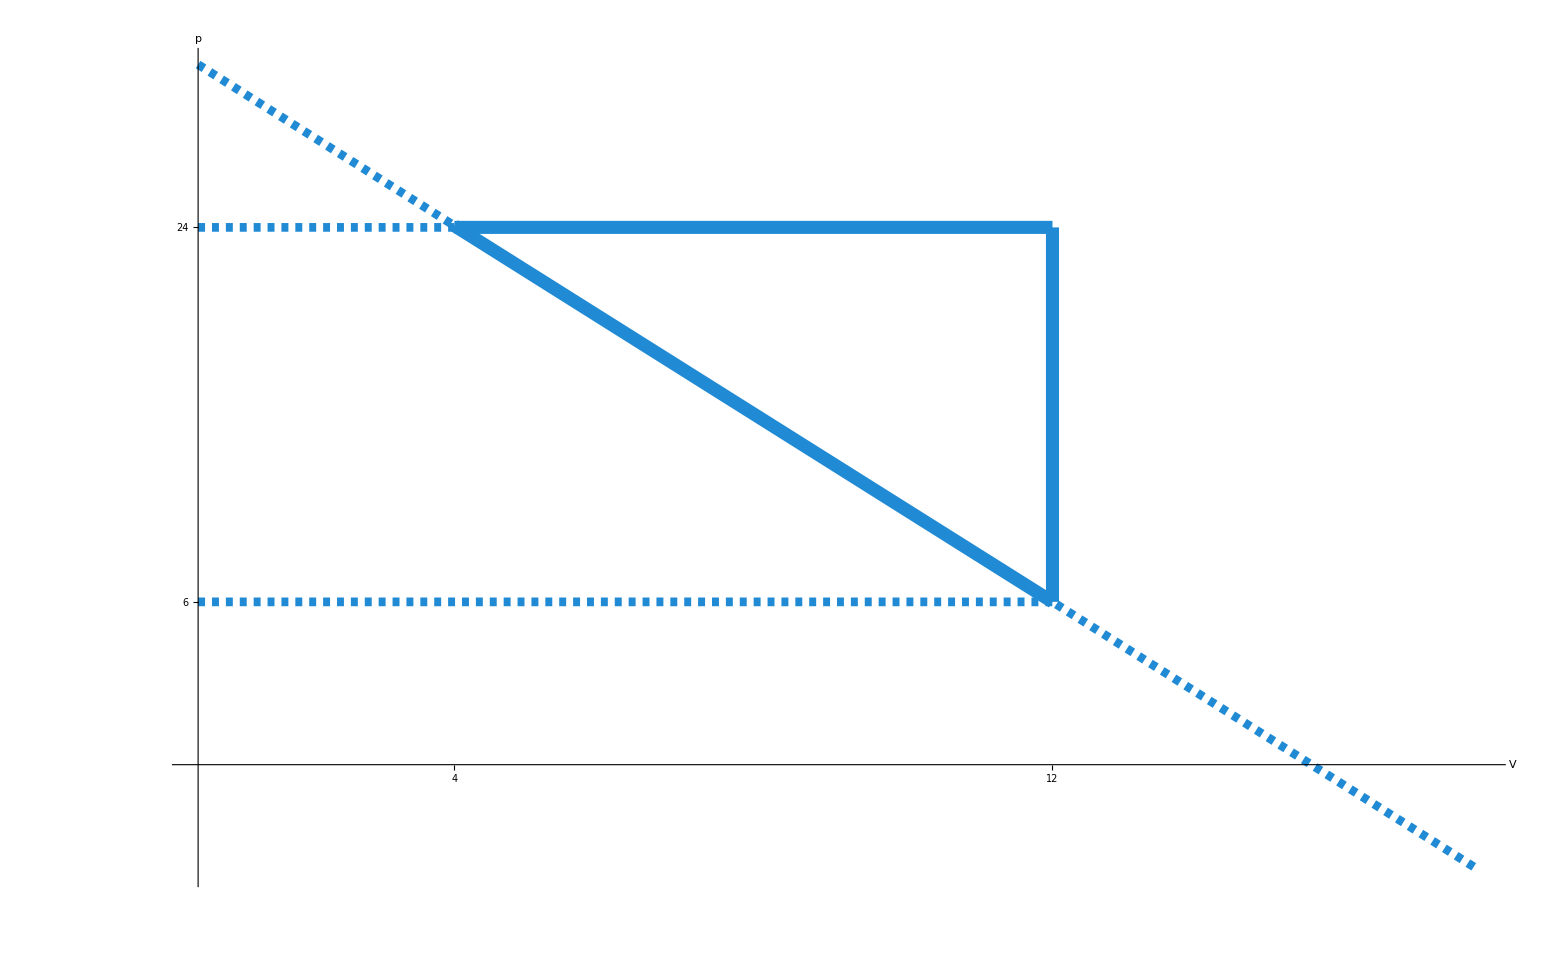

```mathematica
f[x_]:=-3.3x+4.3
g[x_]:=-3.3x+4.3
h[x_]:=3.3
i[x_]:=3.3
j[x_]:=1

Show[{Plot[f[x],{x,0.3,1},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}],Plot[g[x],{x,0,1.5},PlotStyle->{Thickness[0.004],RGBColor["#218ad4"],Dashed}],Plot[i[x],{x,0,0.3},PlotStyle->{Thickness[0.004],RGBColor["#218ad4"],Dashed}],Plot[j[x],{x,0,1},PlotStyle->{Thickness[0.004],RGBColor["#218ad4"],Dashed}],Plot[h[x],{x,0.3,1},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}]},PlotRange->All,AxesOrigin->{0,0},LabelStyle->Directive[Black,50], AxesLabel->{V,p},AxesStyle-> Thick, Epilog->{Thickness[0.006],RGBColor["#218ad4"],Line[{{1,1},{1,3.3}}]},Ticks->{{{0.3,4},{1,12}}, {{1,6},{3.3,24}}},ImageSize->2000]
```

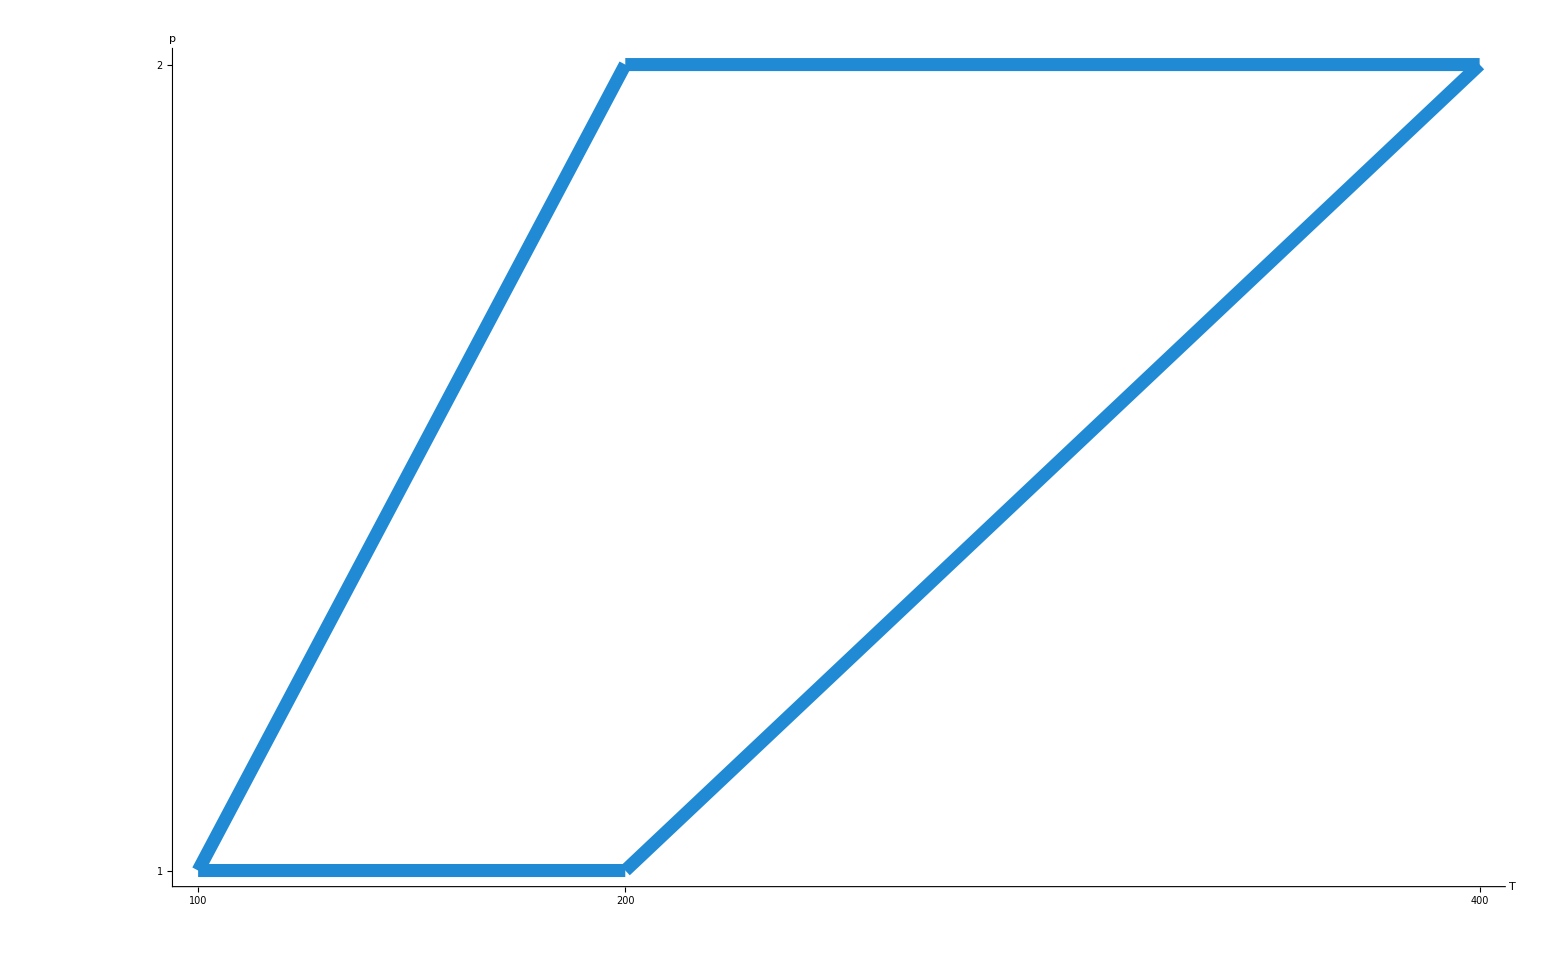

```mathematica
f[x_]:=x
g[x_]:=2
h[x_]:=2x
i[x_]:=1

Show[{Plot[f[x],{x,1,2},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}],Plot[g[x],{x,1,2},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}],Plot[i[x],{x,0.5,1},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}],Plot[h[x],{x,0.5,1},PlotStyle->{Thickness[0.006],RGBColor["#218ad4"]}]},PlotRange->All,AxesOrigin->{0,0},LabelStyle->Directive[Black,50], AxesLabel->{T,p},AxesStyle-> Thick, Ticks->{{{0.5,100},{1,200},{2,400}}, {{1,1},{2,2}}},ImageSize->2000]
```